### Ferromagnetic Layer

Numerically finds Fraunhofer pattern given field in y direction and constant, single-domain magnetization in y direction. Used methods proposed by Blamire et al.

#### Initialize variables

```mathematica
M=3; (*Saturation Magnetization, ignore hysteretic effects*)
bmvector={0,M,0}; (*Magnetization in y direction, unit magnitude*)
bhvector[H_]:={0,H,0}; (*Applied Field in y direction*)
bvecnet[H_]:=bmvector+bhvector[H];
gridsize=5; (*How big an array to work with, for now treating as square*)
bmatrix[H_]:=Table[bvecnet[H],{i,1,gridsize},{j,1,gridsize}];

ϕmatrix[H_]:=Table[Cross[bvecnet[H],{0,0,1}],{i,1,gridsize},{j,1,gridsize}];
```

```mathematica
dx={1/gridsize,0,0};
dy={0,1/gridsize,0};
dz={0,0,1/gridsize}; (*Shouldn't actually need this*)
```

#### Define the phase-dependant current

Right now, uses a parallel sum over the grid, which contains two sums to trace out the path. It would probably be possible to turn this into one big quadruple-sum, which would amost certainly evaluate faster.

```mathematica
Ic[ϕ0_,H_?NumericQ]:=ParallelSum[Sin[ϕ0+Sum[ϕmatrix[H][[i,1]].dx,{i,1,x}]+Sum[ϕmatrix[H][[x,j]].dy,{j,1,y}]],{x,1,gridsize},{y,1,gridsize}]
```

#### Maximize w.r.t. phase to get measured critical current, plot as a function of H

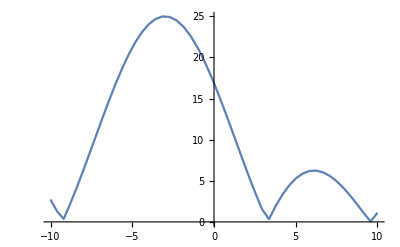
{11.34459,-Graphics-}

```mathematica
Imax[H_?NumericQ]:=NMaxValue[{Ic[ϕ0,H],0≤ϕ0≤2π},ϕ0]
Plot[Imax[Happlied],{Happlied,-10,10},PlotPoints->4,MaxRecursion->4(*By trial and error, these values of PlotPoints and MaxRecursion give much better runtime than default, and good enough resolution*)]//AbsoluteTiming
```